```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.82211},{0.01,-1.78217},{0.02,-1.74385},{0.03,-1.70707},{0.04,-1.67173},{0.05,-1.63776},{0.06,-1.60509},{0.07,-1.57363},{0.08,-1.54334},{0.09,-1.51415},{0.1,-1.48599},{0.11,-1.45882},{0.12,-1.43259},{0.13,-1.40724},{0.14,-1.38274},{0.15,-1.35902},{0.16,-1.33608},{0.17,-1.31384},{0.18,-1.29231},{0.19,-1.27142},{0.2,-1.25115},{0.21,-1.23149},{0.22,-1.21238},{0.23,-1.19382},{0.24,-1.17577},{0.25,-1.15821},{0.26,-1.14114},{0.27,-1.1245},{0.28,-1.1083},{0.29,-1.09252},{0.3,-1.07712},{0.31,-1.06211},{0.32,-1.04749},{0.33,-1.0332},{0.34,-1.01922},{0.35,-1.00555},{0.36,-0.992206},{0.37,-0.979188},{0.38,-0.966481},{0.39,-0.95402},{0.4,-0.94181},{0.41,-0.929856},{0.42,-0.918163},{0.43,-0.906732},{0.44,-0.895516},{0.45,-0.884505},{0.46,-0.873706},{0.47,-0.863125},{0.48,-0.852766},{0.49,-0.842599},{0.5,-0.832604},{0.51,-0.822788},{0.52,-0.813158},{0.53,-0.803715},{0.54,-0.794425},{0.55,-0.785285},{0.56,-0.776305},{0.57,-0.76749},{0.58,-0.758832},{0.59,-0.750299},{0.6,-0.741898},{0.61,-0.733637},{0.62,-0.725521},{0.63,-0.717543},{0.64,-0.709672},{0.65,-0.701913},{0.66,-0.694273},{0.67,-0.68676},{0.68,-0.679375},{0.69,-0.672084},{0.7,-0.66489},{0.71,-0.657801},{0.72,-0.650825},{0.73,-0.643957},{0.74,-0.63717},{0.75,-0.63047},{0.76,-0.623865},{0.77,-0.617363},{0.78,-0.610957},{0.79,-0.60462},{0.8,-0.59836},{0.81,-0.592183},{0.82,-0.586098},{0.83,-0.580106},{0.84,-0.574175},{0.85,-0.568308},{0.86,-0.562513},{0.87,-0.556798},{0.88,-0.551169},{0.89,-0.545611},{0.9,-0.540103},{0.91,-0.534653},{0.92,-0.529269},{0.93,-0.523959},{0.94,-0.518728},{0.95,-0.513548},{0.96,-0.508416},{0.97,-0.50334},{0.98,-0.498328},{0.99,-0.493384},{1.,-0.488487}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.904793},{0.01,-0.908795},{0.02,-0.913012},{0.03,-0.917438},{0.04,-0.922077},{0.05,-0.92693},{0.06,-0.932001},{0.07,-0.93729},{0.08,-0.942802},{0.09,-0.948537},{0.1,-0.954497},{0.11,-0.960693},{0.12,-0.967113},{0.13,-0.973778},{0.14,-0.980676},{0.15,-0.987825},{0.16,-0.995215},{0.17,-1.00286},{0.18,-1.01076},{0.19,-1.01893},{0.2,-1.02736},{0.21,-1.03606},{0.22,-1.04505},{0.23,-1.0543},{0.24,-1.06386},{0.25,-1.07373},{0.26,-1.08387},{0.27,-1.09433},{0.28,-1.10513},{0.29,-1.11624},{0.3,-1.12767},{0.31,-1.13946},{0.32,-1.15162},{0.33,-1.16412},{0.34,-1.17698},{0.35,-1.19024},{0.36,-1.20391},{0.37,-1.21798},{0.38,-1.23243},{0.39,-1.24735},{0.4,-1.26272},{0.41,-1.27854},{0.42,-1.29482},{0.43,-1.31161},{0.44,-1.3289},{0.45,-1.34671},{0.46,-1.36507},{0.47,-1.38399},{0.48,-1.4035},{0.49,-1.42361},{0.5,-1.44434},{0.51,-1.46574},{0.52,-1.4878},{0.53,-1.51058},{0.54,-1.53408},{0.55,-1.55836},{0.56,-1.58342},{0.57,-1.60932},{0.58,-1.63608},{0.59,-1.66374},{0.6,-1.69235},{0.61,-1.72195},{0.62,-1.75258},{0.63,-1.78429},{0.64,-1.81713},{0.65,-1.85117},{0.66,-1.88645},{0.67,-1.92305},{0.68,-1.96103},{0.69,-2.00046},{0.7,-2.04143},{0.71,-2.084},{0.72,-2.12829},{0.73,-2.17438},{0.74,-2.22238},{0.75,-2.27241},{0.76,-2.32458},{0.77,-2.37903},{0.78,-2.4359},{0.79,-2.49535},{0.8,-2.55755},{0.81,-2.6227},{0.82,-2.69099},{0.83,-2.76263},{0.84,-2.8379},{0.85,-2.91704},{0.86,-3.00037},{0.87,-3.0882},{0.88,-3.1809},{0.89,-3.27889},{0.9,-3.38258},{0.91,-3.49255},{0.92,-3.60927},{0.93,-3.73347},{0.94,-3.86578},{0.95,-4.0071},{0.96,-4.15828},{0.97,-4.32045},{0.98,-4.49476},{0.99,-4.68266},{1.,-4.88576}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.13412},{0.01,-1.13104},{0.02,-1.12818},{0.03,-1.12552},{0.04,-1.12307},{0.05,-1.12082},{0.06,-1.11877},{0.07,-1.11691},{0.08,-1.11524},{0.09,-1.11375},{0.1,-1.11245},{0.11,-1.11132},{0.12,-1.11038},{0.13,-1.1096},{0.14,-1.109},{0.15,-1.10856},{0.16,-1.10829},{0.17,-1.10818},{0.18,-1.10823},{0.19,-1.10844},{0.2,-1.1088},{0.21,-1.10932},{0.22,-1.10999},{0.23,-1.11081},{0.24,-1.11178},{0.25,-1.11288},{0.26,-1.11414},{0.27,-1.11554},{0.28,-1.11708},{0.29,-1.11876},{0.3,-1.12058},{0.31,-1.12253},{0.32,-1.12462},{0.33,-1.12685},{0.34,-1.12921},{0.35,-1.1317},{0.36,-1.13431},{0.37,-1.13707},{0.38,-1.13996},{0.39,-1.14298},{0.4,-1.14611},{0.41,-1.14938},{0.42,-1.15279},{0.43,-1.15632},{0.44,-1.15997},{0.45,-1.16374},{0.46,-1.16765},{0.47,-1.17169},{0.48,-1.17586},{0.49,-1.18014},{0.5,-1.18454},{0.51,-1.18908},{0.52,-1.19374},{0.53,-1.19854},{0.54,-1.20346},{0.55,-1.20849},{0.56,-1.21365},{0.57,-1.21895},{0.58,-1.22438},{0.59,-1.22993},{0.6,-1.23561},{0.61,-1.24141},{0.62,-1.24734},{0.63,-1.25341},{0.64,-1.25961},{0.65,-1.26595},{0.66,-1.27241},{0.67,-1.279},{0.68,-1.28572},{0.69,-1.29259},{0.7,-1.29959},{0.71,-1.30672},{0.72,-1.31399},{0.73,-1.32141},{0.74,-1.32896},{0.75,-1.33665},{0.76,-1.34449},{0.77,-1.35247},{0.78,-1.3606},{0.79,-1.36887},{0.8,-1.37729},{0.81,-1.38587},{0.82,-1.3946},{0.83,-1.40348},{0.84,-1.41251},{0.85,-1.4217},{0.86,-1.43106},{0.87,-1.44057},{0.88,-1.45025},{0.89,-1.46009},{0.9,-1.4701},{0.91,-1.48029},{0.92,-1.49064},{0.93,-1.50117},{0.94,-1.51188},{0.95,-1.52277},{0.96,-1.53384},{0.97,-1.5451},{0.98,-1.55655},{0.99,-1.56818},{1.,-1.58002}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.59278},{0.01,-1.56769},{0.02,-1.54344},{0.03,-1.52},{0.04,-1.49732},{0.05,-1.47539},{0.06,-1.45415},{0.07,-1.4336},{0.08,-1.41367},{0.09,-1.39437},{0.1,-1.37565},{0.11,-1.3575},{0.12,-1.33988},{0.13,-1.32278},{0.14,-1.30617},{0.15,-1.29003},{0.16,-1.27434},{0.17,-1.25908},{0.18,-1.24424},{0.19,-1.22979},{0.2,-1.21573},{0.21,-1.20202},{0.22,-1.18866},{0.23,-1.17563},{0.24,-1.16295},{0.25,-1.15056},{0.26,-1.13846},{0.27,-1.12665},{0.28,-1.11513},{0.29,-1.10386},{0.3,-1.09284},{0.31,-1.08206},{0.32,-1.07154},{0.33,-1.06122},{0.34,-1.05113},{0.35,-1.04124},{0.36,-1.03157},{0.37,-1.02209},{0.38,-1.01278},{0.39,-1.00367},{0.4,-0.994734},{0.41,-0.985972},{0.42,-0.977362},{0.43,-0.968909},{0.44,-0.960615},{0.45,-0.95248},{0.46,-0.944482},{0.47,-0.936614},{0.48,-0.928879},{0.49,-0.92128},{0.5,-0.91382},{0.51,-0.906475},{0.52,-0.89924},{0.53,-0.892117},{0.54,-0.88511},{0.55,-0.878222},{0.56,-0.871444},{0.57,-0.864755},{0.58,-0.85816},{0.59,-0.851661},{0.6,-0.845262},{0.61,-0.838967},{0.62,-0.832756},{0.63,-0.826623},{0.64,-0.82057},{0.65,-0.814603},{0.66,-0.808725},{0.67,-0.802927},{0.68,-0.797194},{0.69,-0.791531},{0.7,-0.785941},{0.71,-0.780429},{0.72,-0.774996},{0.73,-0.76962},{0.74,-0.764301},{0.75,-0.759045},{0.76,-0.753854},{0.77,-0.748733},{0.78,-0.74368},{0.79,-0.738673},{0.8,-0.733716},{0.81,-0.728812},{0.82,-0.723965},{0.83,-0.719181},{0.84,-0.714457},{0.85,-0.709775},{0.86,-0.705135},{0.87,-0.700543},{0.88,-0.696003},{0.89,-0.691519},{0.9,-0.68708},{0.91,-0.682678},{0.92,-0.678317},{0.93,-0.674},{0.94,-0.669733},{0.95,-0.665514},{0.96,-0.661327},{0.97,-0.657175},{0.98,-0.653061},{0.99,-0.64899},{1.,-0.644966}}

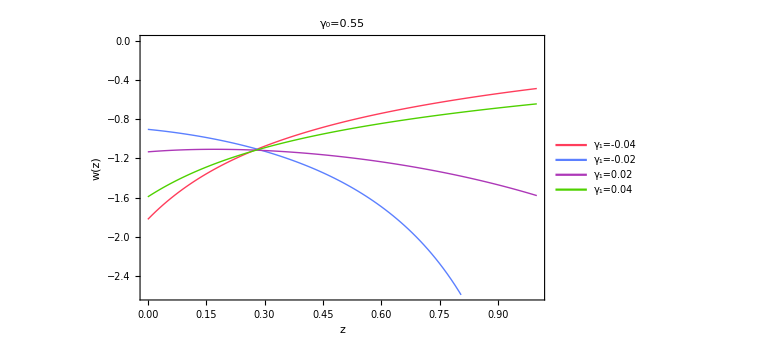

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55", Black, FontSize->20]]
```